```mathematica
Clear["Global`*"]
vf=14000;
vi=0;
a=9.81*800;
Solve[vf^2==vi^2+2 a x*1000]
```

{{x→12.4873}}

```mathematica
ρC=.0005("kg")/("m")^3;
v=20("m")/("s");
A=2000"m"*1000"m";
mFlow=ρC*v*A;
η=.1;
pUsage=(3832000000000"kW""hr")/(365.25*24"hr");
Solve[pUsage==1/2 ρC*A*v^3*η*(1 "kW")/(1000("kg" ("m")^2)/("s")^3)*n,n][[-1]][[-1]]
```

n→1.09286×10^6

1.01937

```mathematica
2000*2000
```

4000000

```mathematica
Clear["Global`*"]

(*g=32.2;*)
v[y_]:=√(2g y)
A[y_]:=π r^2
A[y] ⅆy/ⅆt==-a v[y];
∫A[y]/v[y] ⅆy==∫-a ⅆt+C[1];

a==(30*10^6)/(.5 1000 9.81 200 30);
2 π r^2 √yBegin==-√(2g)a tBegin+C[1];

C[1]==2 π r^2 √yBegin+√(2g)a tBegin;

aHole=Solve[2 π r^2 √y==-√(2g)a t+(2 π r^2 √yBegin+√(2g)a tBegin)/.{y->yMiddle,t->tMiddle},a][[-1]][[-1]];

tEnd==(2 π r^2 √yEnd-(2 π r^2 √yBegin+√(2g)a tBegin))/(-√(2g)a)/.{aHole};



tEnd==((tBegin-tMiddle) (-2 π r^2 √yBegin+2 π r^2 √yEnd+(2 tBegin (π r^2 √yBegin-π r^2 √yMiddle))/(tBegin-tMiddle)))/(2 (π r^2 √yBegin-π r^2 √yMiddle))/.{tBegin->0,yEnd->0};


Solve[tEnd==(π r^2 tMiddle √yBegin)/(π r^2 √yBegin-π r^2 √(-(1. (-0.516 tMiddle^2+1.4372 r^2 tMiddle √yBegin- r^4 yBegin))/r^4)),yBegin];
{{yBegin->(0.5 (-(1. tEnd^2 (-1.2909649*^7 tEnd^2+1.29*^7 tEnd tMiddle-6.45*^6 tMiddle^2))/r^4-(1. √(1.66659037303201*^14 tEnd^8-3.330689442*^14 tEnd^7 tMiddle+1.665344721*^14 tEnd^6 tMiddle^2))/r^4))/(2.5*^7 tEnd^2-2.5*^7 tEnd tMiddle+6.25*^6 tMiddle^2)},{yBegin->(0.5 (-(1. tEnd^2 (-1.2909649*^7 tEnd^2+1.29*^7 tEnd tMiddle-6.45*^6 tMiddle^2))/r^4+(√(1.66659037303201*^14 tEnd^8-3.330689442*^14 tEnd^7 tMiddle+1.665344721*^14 tEnd^6 tMiddle^2))/r^4))/(2.5*^7 tEnd^2-2.5*^7 tEnd tMiddle+6.25*^6 tMiddle^2)}}/.{tEnd->3600 24 7,r->200,tMiddle->3600 24 4}





Solve[(30*10^6)/(.5 1000 9.81 200 30)==-(√2 (π r^2 √yBegin-π r^2 √yMiddle))/(√9.81 (0-tMiddle)),yMiddle];
```

{{yBegin→18.8415},{yBegin→118.171}}

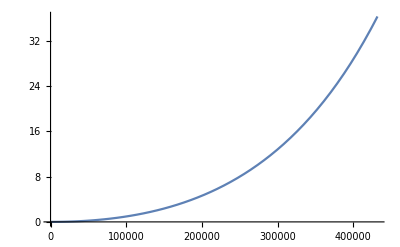

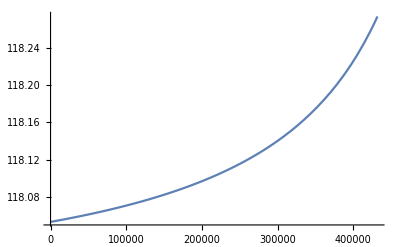

```mathematica
Plot[(0.5 (-228.614(-4.72213065655296*^18+7.80192*^12 tMiddle-6.45*^6 tMiddle^2)-6.25*^-10 √(2.9834799855886003*^60-9.858631140102745*^54 tMiddle+8.15032336318018*^48 tMiddle^2)))/(9.144576*^18-1.512*^13 tMiddle+6.25*^6 tMiddle^2),{tMiddle,0,3600*24*5}]
Plot[(0.5 (-228.6144(-4.72213065655296*^18+7.80192*^12 tMiddle-6.45*^6 tMiddle^2)+(√(2.9834799855886003*^60-9.858631140102745*^54 tMiddle+8.15032336318018*^48 tMiddle^2))/1600000000))/(9.144576*^18-1.512*^13 tMiddle+6.25*^6 tMiddle^2),{tMiddle,0,3600*24*5}]
```